```mathematica
GraphOfGraphs[G_]:=Graph[G,VertexLabels->MapIndexed[#->Placed[{VertexList[G][[#2[[1]]]]},{Tooltip}]&,VertexList[G]]]
PerfectDistanceQ[G_]:=(Union@*Flatten@*Round@GraphDistanceMatrix[G] == Range[0,Binomial[VertexCount[G],2]])∧(SubsetQ[Range[Binomial[VertexCount[G],2]],AnnotationValue[G,EdgeWeight]]);
NoNewVertex[G_]:=Complement[(#1<->#2&@@@Subsets[VertexList[G],{2}]),EdgeList[G]]
OneNewVertex[G_]:=#<->(VertexCount[G]+1)&/@ VertexList[G]
TwoNewVertex[G_]:={(VertexCount[G]+1)<->(VertexCount[G]+2)}

NewEdges[G_]:= NoNewVertex[G]∪OneNewVertex[G]∪TwoNewVertex[G]

NextWeight[G_]:=
Module[{distances,nextWeight},
distances =DeleteCases[Union@*Flatten@*Round@*GraphDistanceMatrix@*Graph@G,0];nextWeight = 1;While[(nextWeight<=Length[distances])∧(distances[[nextWeight]]==nextWeight),nextWeight++];
nextWeight
]

AddWeightedEdge[G_,e_,w_]:=Graph[EdgeAdd[G,e],EdgeWeight->Append[AnnotationValue[G,EdgeWeight],w]] (*add edge e to G with weight w*)

(*IsomorphicWeightingQ[G1_,G2_]:=If[LineGraph[G1]==LineGraph[G2],True,False]*)

ChildrenNoReduce[G_]:=AddWeightedEdge[G,#,NextWeight[G]]&/@NewEdges[G];
Children[G_]:=Select[ChildrenNoReduce[G],DuplicateFreeQ[AnnotationValue[#,EdgeWeight]]&];
ChildrenEdges[G_]:=G<->#&/@Children[G] ;(*Used to add new graphs to search Tree*)
```

```mathematica
Gstart = Graph[{1<->2},EdgeWeight->{1<->2->1}];
searchTree = Graph[{Gstart},{}];
Leaves = {Gstart};
```

11




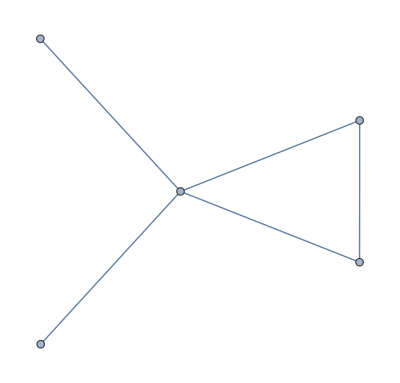
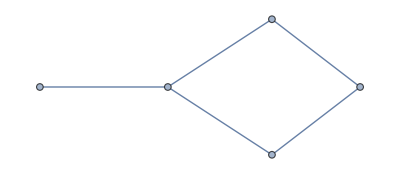
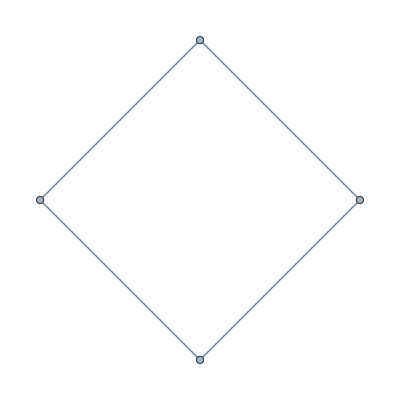
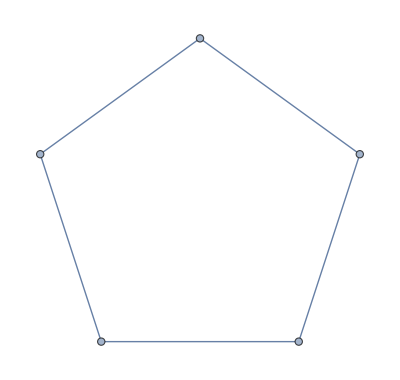
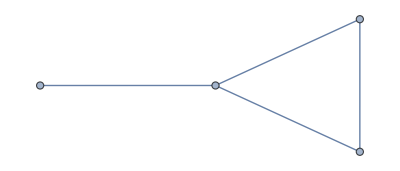
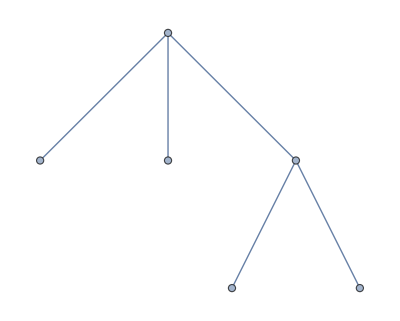
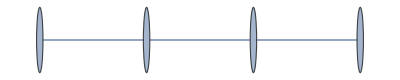
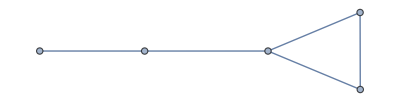

```mathematica
edgesToAdd = Flatten[ChildrenEdges/@Leaves];
Leaves = Last/@edgesToAdd;
searchTree =EdgeAdd[searchTree,edgesToAdd];


PDGs={};
DepthFirstScan[searchTree, Gstart, {"PrevisitVertex"->(If[PerfectDistanceQ[#],AppendTo[PDGs,#]];&)}];
PDGReduced = DeleteDuplicatesBy[PDGs,CanonicalGraph];
Length[PDGReduced]
PDGReduced
```

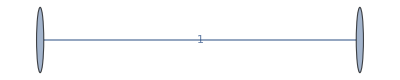
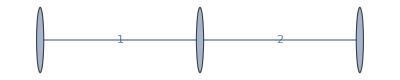
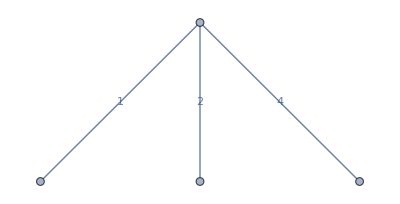
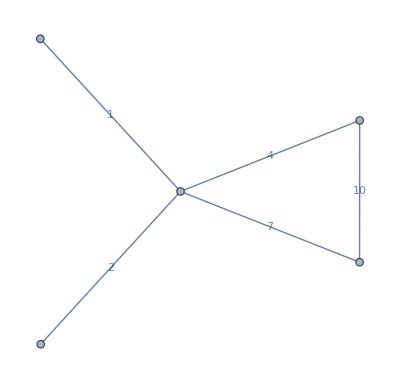
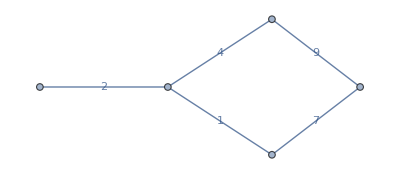
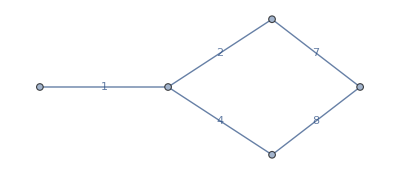
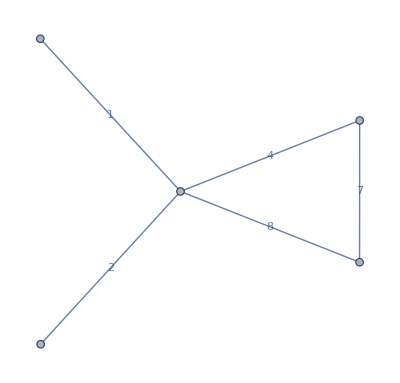
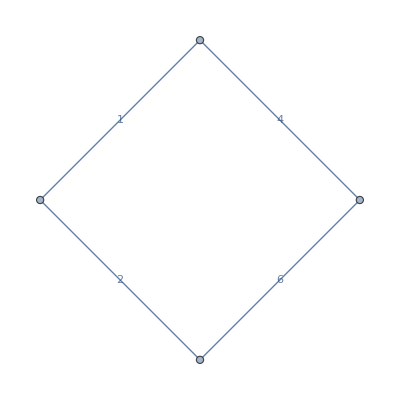

```mathematica
GatherBy[Graph[#,EdgeLabels->"EdgeWeight"]&/@PDGs,LineGraph]
```